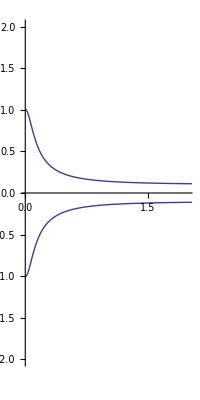

```mathematica
ParametricPlot[{Re[h[t]],Im[h[t]]},{t,-4,4},
	PlotRange->{{-0,2},{-2,2}}]
```

```mathematica
h[t_]:=Sqrt[(Re[t]+Im[t]+0.1I)^2-1]
```

```mathematica
x+ⅈ x
```

```mathematica
Simplify[Sqrt[(x+y I)^2],y>0]
```

√((x+ⅈ y)^2)

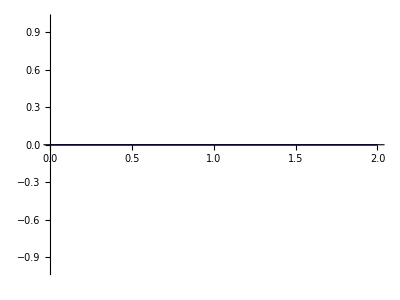

```mathematica
ParametricPlot[{Re[Sqrt[x^2]],Im[Sqrt[x^2]]},{x,-2,2}]
```

```mathematica
Solve[(1+2 I)^(1/3)-x==0,x]
```

{{x→(1+2 ⅈ)^(1/3)}}

```mathematica
Solve[(x+y I)^(1/3) == 0, {x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→-ⅈ y}}

```mathematica
Simplify[x^2==(1+2I),]
```

{{x→-√(1+2 ⅈ)},{x→√(1+2 ⅈ)}}

```mathematica
Element[5,Primes]
```

True

```mathematica
Maximize[x*x-999y==1,x]
```

```mathematica
Maximize[x^2-D y==1,x]
```

```mathematica
Maximize[x^2-D y==1]
```

```mathematica
FindInstance[x^2-D y==1,{x,y,D},Integers&&D>0]
```

FindInstance::bddom: Value Integers && D > 0 of the domain argument should be Complexes, Reals, Algebraics, Rationals, Integers, Primes, Booleans, or Automatic.

```mathematica
FindInstance[x^2-D y==1,{x,y,D},Integer&&D>0]
```

FindInstance::bddom: Value Integer && D > 0 of the domain argument should be Complexes, Reals, Algebraics, Rationals, Integers, Primes, Booleans, or Automatic.

```mathematica
Maximize[{x^2+13y==1,x>0,y >0},{x,y},Integers]
```

```mathematica
FindInstance[{x^2-13 y^2==1,x>0,y>0},{x,y},Integers]
```

{{x→649,y→180},{x→6787570465375238075075157060001,y→1882533334518107155172472208200}}

```mathematica
Maximize[{x^2==1+999 y,x>0,y>0},{x,y},Integers]
```

```mathematica
Maximize[{x^2-999 y==1,x>0,y>0},{x},Integers]
```

```mathematica
Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
SquareFreeQ[16]
```

False

```mathematica
dio[D_] :=List[D,FindInstance[{x^2-D y^2==1,x>0,y>0},{x,y},Integers]]
```

```mathematica
dio[11]
```

{11,{{x→10,y→3}}}

```mathematica
Map[dio,Select[Range[1,1000],SquareFreeQ]]
```

{{1,{}},{2,{{x→3,y→2}}},{3,{{x→2,y→1}}},{5,{{x→9,y→4}}},{6,{{x→5,y→2}}},{7,{{x→8,y→3}}},{10,{{x→19,y→6}}},{11,{{x→10,y→3}}},{13,{{x→649,y→180}}},{14,{{x→15,y→4}}},{15,{{x→4,y→1}}},{17,{{x→33,y→8}}},{19,{{x→170,y→39}}},{21,{{x→55,y→12}}},{22,{{x→197,y→42}}},{23,{{x→24,y→5}}},{26,{{x→51,y→10}}},{29,{{x→9801,y→1820}}},{30,{{x→11,y→2}}},{31,{{x→1520,y→273}}},{33,{{x→23,y→4}}},{34,{{x→35,y→6}}},{35,{{x→6,y→1}}},{37,{{x→73,y→12}}},{38,{{x→37,y→6}}},{39,{{x→25,y→4}}},{41,{{x→2049,y→320}}},{42,{{x→13,y→2}}},{43,{{x→3482,y→531}}},{46,{{x→24335,y→3588}}},{47,{{x→48,y→7}}},{51,{{x→50,y→7}}},{53,{{x→66249,y→9100}}},{55,{{x→89,y→12}}},{57,{{x→151,y→20}}},{58,{{x→19603,y→2574}}},{59,{{x→530,y→69}}},{61,{{x→1766319049,y→226153980}}},{62,{{x→63,y→8}}},{65,{{x→129,y→16}}},{66,{{x→65,y→8}}},{67,{{x→48842,y→5967}}},{69,{{x→7775,y→936}}},{70,{{x→251,y→30}}},{71,{{x→3480,y→413}}},{73,{{x→2281249,y→267000}}},{74,{{x→3699,y→430}}},{77,{{x→351,y→40}}},{78,{{x→53,y→6}}},{79,{{x→80,y→9}}},{82,{{x→163,y→18}}},{83,{{x→82,y→9}}},{85,{{x→285769,y→30996}}},{86,{{x→10405,y→1122}}},{87,{{x→28,y→3}}},{89,{{x→500001,y→53000}}},{91,{{x→1574,y→165}}},{93,{{x→12151,y→1260}}},{94,{{x→2143295,y→221064}}},{95,{{x→39,y→4}}},{97,{{x→62809633,y→6377352}}},{101,{{x→201,y→20}}},{102,{{x→101,y→10}}},{103,{{x→227528,y→22419}}},{105,{{x→41,y→4}}},{106,{{x→32080051,y→3115890}}},{107,{{x→962,y→93}}},{109,{{x→158070671986249,y→15140424455100}}},{110,{{x→21,y→2}}},{111,{{x→295,y→28}}},{113,{{x→1204353,y→113296}}},{114,{{x→1025,y→96}}},{115,{{x→1126,y→105}}},{118,{{x→306917,y→28254}}},{119,{{x→120,y→11}}},{122,{{x→243,y→22}}},{123,{{x→122,y→11}}},{127,{{x→4730624,y→419775}}},{129,{{x→16855,y→1484}}},{130,{{x→6499,y→570}}},{131,{{x→10610,y→927}}},{133,{{x→2588599,y→224460}}},{134,{{x→145925,y→12606}}},{137,{{x→6083073,y→519712}}},{138,{{x→47,y→4}}},{139,{{x→77563250,y→6578829}}},{141,{{x→95,y→8}}},{142,{{x→143,y→12}}},{143,{{x→12,y→1}}},{145,{{x→289,y→24}}},{146,{{x→145,y→12}}},{149,{{x→25801741449,y→2113761020}}},{151,{{x→1728148040,y→140634693}}},{154,{{x→21295,y→1716}}},{155,{{x→249,y→20}}},{157,{{x→46698728731849,y→3726964292220}}},{158,{{x→7743,y→616}}},{159,{{x→1324,y→105}}},{161,{{x→11775,y→928}}},{163,{{x→64080026,y→5019135}}},{165,{{x→1079,y→84}}},{166,{{x→1700902565,y→132015642}}},{167,{{x→168,y→13}}},{170,{{x→339,y→26}}},{173,{{x→2499849,y→190060}}},{174,{{x→1451,y→110}}},{177,{{x→62423,y→4692}}},{178,{{x→1601,y→120}}},{179,{{x→4190210,y→313191}}},{181,{{x→2469645423824185801,y→183567298683461940}}},{182,{{x→27,y→2}}},{183,{{x→487,y→36}}},{185,{{x→9249,y→680}}},{186,{{x→7501,y→550}}},{187,{{x→1682,y→123}}},{190,{{x→52021,y→3774}}},{191,{{x→8994000,y→650783}}},{193,{{x→6224323426849,y→448036604040}}},{194,{{x→195,y→14}}},{195,{{x→14,y→1}}},{197,{{x→393,y→28}}},{199,{{x→16266196520,y→1153080099}}},{201,{{x→515095,y→36332}}},{202,{{x→19731763,y→1388322}}},{203,{{x→57,y→4}}},{205,{{x→39689,y→2772}}},{206,{{x→59535,y→4148}}},{209,{{x→46551,y→3220}}},{210,{{x→29,y→2}}},{211,{{x→278354373650,y→19162705353}}},{213,{{x→194399,y→13320}}},{214,{{x→695359189925,y→47533775646}}},{215,{{x→44,y→3}}},{217,{{x→3844063,y→260952}}},{218,{{x→126003,y→8534}}},{219,{{x→74,y→5}}},{221,{{x→1665,y→112}}},{222,{{x→149,y→10}}},{223,{{x→224,y→15}}},{226,{{x→451,y→30}}},{227,{{x→226,y→15}}},{229,{{x→5848201,y→386460}}},{230,{{x→91,y→6}}},{231,{{x→76,y→5}}},{233,{{x→1072400673,y→70255304}}},{235,{{x→46,y→3}}},{237,{{x→228151,y→14820}}},{238,{{x→11663,y→756}}},{239,{{x→6195120,y→400729}}},{241,{{x→10085143557001249,y→649641205044600}}},{246,{{x→88805,y→5662}}},{247,{{x→85292,y→5427}}},{249,{{x→8553815,y→542076}}},{251,{{x→3674890,y→231957}}},{253,{{x→3222617399,y→202604220}}},{254,{{x→255,y→16}}},{255,{{x→16,y→1}}},{257,{{x→513,y→32}}},{258,{{x→257,y→16}}},{259,{{x→847225,y→52644}}},{262,{{x→104980517,y→6485718}}},{263,{{x→139128,y→8579}}},{265,{{x→73738369,y→4529712}}},{266,{{x→685,y→42}}},{267,{{x→2402,y→147}}},{269,{{x→13449,y→820}}},{271,{{x→115974983600,y→7044978537}}},{273,{{x→727,y→44}}},{274,{{x→3959299,y→239190}}},{277,{{x→159150073798980475849,y→9562401173878027020}}},{278,{{x→2501,y→150}}},{281,{{x→2262200630049,y→134951575480}}},{282,{{x→2351,y→140}}},{283,{{x→138274082,y→8219541}}},{285,{{x→2431,y→144}}},{286,{{x→561835,y→33222}}},{287,{{x→288,y→17}}},{290,{{x→579,y→34}}},{291,{{x→290,y→17}}},{293,{{x→12320649,y→719780}}},{295,{{x→2024999,y→117900}}},{298,{{x→335473872499,y→19433479650}}},{299,{{x→415,y→24}}},{301,{{x→5883392537695,y→339113108232}}},{302,{{x→4276623,y→246092}}},{303,{{x→2524,y→145}}},{305,{{x→489,y→28}}},{307,{{x→88529282,y→5052633}}},{309,{{x→64202725495,y→3652365444}}},{310,{{x→848719,y→48204}}},{311,{{x→16883880,y→957397}}},{313,{{x→32188120829134849,y→1819380158564160}}},{314,{{x→392499,y→22150}}},{317,{{x→248678907849,y→13967198980}}},{318,{{x→107,y→6}}},{319,{{x→12901780,y→722361}}},{321,{{x→215,y→12}}},{322,{{x→323,y→18}}},{323,{{x→18,y→1}}},{326,{{x→325,y→18}}},{327,{{x→217,y→12}}},{329,{{x→2376415,y→131016}}},{330,{{x→109,y→6}}},{331,{{x→2785589801443970,y→153109862634573}}},{334,{{x→63804373719695,y→3491219999244}}},{335,{{x→604,y→33}}},{337,{{x→2063810353129713793,y→112422913565764752}}},{339,{{x→97970,y→5321}}},{341,{{x→10626551,y→575460}}},{345,{{x→6761,y→364}}},{346,{{x→17299,y→930}}},{347,{{x→641602,y→34443}}},{349,{{x→169648201,y→9081060}}},{353,{{x→10157115393,y→540608704}}},{354,{{x→258065,y→13716}}},{355,{{x→954809,y→50676}}},{357,{{x→3401,y→180}}},{358,{{x→176579805797,y→9332532726}}},{359,{{x→360,y→19}}},{362,{{x→723,y→38}}},{365,{{x→23915529,y→1251796}}},{366,{{x→907925,y→47458}}},{367,{{x→19019995568,y→992835687}}},{370,{{x→213859,y→11118}}},{371,{{x→1695,y→88}}},{373,{{x→52387849,y→2712540}}},{374,{{x→3365,y→174}}},{377,{{x→233,y→12}}},{379,{{x→12941197220540690,y→664744650125541}}},{381,{{x→1015,y→52}}},{382,{{x→164998439999,y→8442054600}}},{383,{{x→18768,y→959}}},{385,{{x→95831,y→4884}}},{386,{{x→111555,y→5678}}},{389,{{x→3287049,y→166660}}},{390,{{x→79,y→4}}},{391,{{x→7338680,y→371133}}},{393,{{x→46437143,y→2342444}}},{394,{{x→312086396361222451,y→15722685507826110}}},{395,{{x→159,y→8}}},{397,{{x→838721786045180184649,y→42094239791738433660}}},{398,{{x→399,y→20}}},{399,{{x→20,y→1}}},{401,{{x→801,y→40}}},{402,{{x→401,y→20}}},{403,{{x→669878,y→33369}}},{406,{{x→59468095,y→2951352}}},{407,{{x→2663,y→132}}},{409,{{x→25052977273092427986049,y→1238789998647218582160}}},{410,{{x→81,y→4}}},{411,{{x→49730,y→2453}}},{413,{{x→113399,y→5580}}},{415,{{x→18412804,y→903849}}},{417,{{x→85322647,y→4178268}}},{418,{{x→33857,y→1656}}},{419,{{x→270174970,y→13198911}}},{421,{{x→3879474045914926879468217167061449,y→189073995951839020880499780706260}}},{422,{{x→7022501,y→341850}}},{426,{{x→88751,y→4300}}},{427,{{x→62,y→3}}},{429,{{x→1524095,y→73584}}},{430,{{x→2862251,y→138030}}},{431,{{x→151560720,y→7300423}}},{433,{{x→104564907854286695713,y→5025068784834899736}}},{434,{{x→125,y→6}}},{435,{{x→146,y→7}}},{437,{{x→4599,y→220}}},{438,{{x→293,y→14}}},{439,{{x→440,y→21}}},{442,{{x→883,y→42}}},{443,{{x→442,y→21}}},{445,{{x→43468489,y→2060604}}},{446,{{x→110166015,y→5216512}}},{447,{{x→148,y→7}}},{449,{{x→71798771299708449,y→3388393513402120}}},{451,{{x→46471490,y→2188257}}},{453,{{x→1653751,y→77700}}},{454,{{x→16916040084175685,y→793909098494766}}},{455,{{x→64,y→3}}},{457,{{x→6983244756398928218113,y→326662411570389853632}}},{458,{{x→22899,y→1070}}},{461,{{x→1182351890184201,y→55067617520620}}},{462,{{x→43,y→2}}},{463,{{x→247512720456368,y→11502891625161}}},{465,{{x→15871,y→736}}},{466,{{x→938319425,y→43466808}}},{467,{{x→1625626,y→75225}}},{469,{{x→137215,y→6336}}},{470,{{x→1691,y→78}}},{471,{{x→7838695,y→361188}}},{473,{{x→87,y→4}}},{474,{{x→193549,y→8890}}},{478,{{x→1617319577991743,y→73974475657896}}},{479,{{x→2989440,y→136591}}},{481,{{x→1859131879201,y→84769117080}}},{482,{{x→483,y→22}}},{483,{{x→22,y→1}}},{485,{{x→969,y→44}}},{487,{{x→51906073840568,y→2352088722477}}},{489,{{x→7592629975,y→343350596}}},{491,{{x→93628044170,y→4225374483}}},{493,{{x→935662752649,y→42140131020}}},{494,{{x→73035,y→3286}}},{497,{{x→1201887,y→53912}}},{498,{{x→179777,y→8056}}},{499,{{x→4490,y→201}}},{501,{{x→11242731902975,y→502288218432}}},{502,{{x→3832352837,y→171046278}}},{503,{{x→24648,y→1099}}},{505,{{x→809,y→36}}},{506,{{x→45,y→2}}},{509,{{x→313201220822405001,y→13882400040814700}}},{510,{{x→271,y→12}}},{511,{{x→4188548960,y→185290497}}},{514,{{x→4625,y→204}}},{515,{{x→17406,y→767}}},{517,{{x→590968985399,y→25990786260}}},{518,{{x→2367,y→104}}},{519,{{x→14851876,y→651925}}},{521,{{x→32961431500035201,y→1444066532654320}}},{523,{{x→81810300626,y→3577314675}}},{526,{{x→84056091546952933775,y→3665019757324295532}}},{527,{{x→528,y→23}}},{530,{{x→1059,y→46}}},{533,{{x→74859849,y→3242540}}},{534,{{x→3678725,y→159194}}},{535,{{x→1618804,y→69987}}},{537,{{x→192349463,y→8300492}}},{538,{{x→9536081203,y→411129654}}},{541,{{x→3707453360023867028800645599667005001,y→159395869721270110077187138775196900}}},{542,{{x→4293183,y→184408}}},{543,{{x→669337,y→28724}}},{545,{{x→1961,y→84}}},{546,{{x→701,y→30}}},{547,{{x→160177601264642,y→6848699678673}}},{551,{{x→8380,y→357}}},{553,{{x→624635837407,y→26562217704}}},{554,{{x→60756099699,y→2581279330}}},{555,{{x→1814,y→77}}},{557,{{x→27849,y→1180}}},{559,{{x→506568295,y→21425556}}},{561,{{x→522785,y→22072}}},{562,{{x→220938497,y→9319728}}},{563,{{x→68122,y→2871}}},{565,{{x→435259412378569,y→18311501103948}}},{566,{{x→95609285,y→4018758}}},{569,{{x→16760473211643448449,y→702635588524014320}}},{570,{{x→191,y→8}}},{571,{{x→181124355061630786130,y→7579818350628982587}}},{573,{{x→383,y→16}}},{574,{{x→575,y→24}}},{577,{{x→1153,y→48}}},{579,{{x→385,y→16}}},{581,{{x→152071153975,y→6308974548}}},{582,{{x→193,y→8}}},{583,{{x→8429543,y→349116}}},{586,{{x→33867877212256207699,y→1399069112058008310}}},{587,{{x→1907162,y→78717}}},{589,{{x→41423166067036218751,y→1706811823063746000}}},{590,{{x→5781,y→238}}},{591,{{x→165676,y→6815}}},{593,{{x→721517598849,y→29629176560}}},{595,{{x→18514,y→759}}},{597,{{x→463287093751,y→18961078500}}},{598,{{x→1574351,y→64380}}},{599,{{x→24686379794520,y→1008658133851}}},{601,{{x→38902815462492318420311478049,y→1586878942101888360258625080}}},{602,{{x→687,y→28}}},{606,{{x→42187499,y→1713750}}},{607,{{x→164076033968,y→6659640783}}},{609,{{x→605695,y→24544}}},{610,{{x→10323982819,y→418005846}}},{611,{{x→236926,y→9585}}},{613,{{x→464018873584078278910994299849,y→18741545784831997880308784340}}},{614,{{x→348291186245,y→14055888354}}},{615,{{x→124,y→5}}},{617,{{x→3363593612801313,y→135413180018248}}},{618,{{x→10093,y→406}}},{619,{{x→517213510553282930,y→20788566180548739}}},{622,{{x→13804370063,y→553504812}}},{623,{{x→624,y→25}}},{626,{{x→1251,y→50}}},{627,{{x→626,y→25}}},{629,{{x→123245001,y→4914100}}},{631,{{x→48961575312998650035560,y→1949129537575151036427}}},{633,{{x→440772247,y→17519124}}},{634,{{x→8711856945587257031251,y→345992039259400361250}}},{635,{{x→126,y→5}}},{638,{{x→42283,y→1674}}},{641,{{x→2609429220845977814049,y→103066257550962737720}}},{642,{{x→5777,y→228}}},{643,{{x→1988960193026,y→78436933185}}},{645,{{x→1024001,y→40320}}},{646,{{x→305,y→12}}},{647,{{x→120187368,y→4725053}}},{649,{{x→1123593226162199,y→44104892095380}}},{651,{{x→1735,y→68}}},{653,{{x→10499986568677299849,y→410896226494013260}}},{654,{{x→8915765,y→348634}}},{655,{{x→737709209,y→28824684}}},{658,{{x→1693,y→66}}},{659,{{x→5930,y→231}}},{661,{{x→16421658242965910275055840472270471049,y→638728478116949861246791167518480580}}},{662,{{x→1718102501,y→66775950}}},{663,{{x→103,y→4}}},{665,{{x→13719,y→532}}},{667,{{x→107119097,y→4147668}}},{669,{{x→14226117859054135,y→550013492618436}}},{670,{{x→5791211,y→223734}}},{671,{{x→58620,y→2263}}},{673,{{x→4765506835465395993032041249,y→183696788896587421699032600}}},{674,{{x→675,y→26}}},{677,{{x→1353,y→52}}},{678,{{x→677,y→26}}},{679,{{x→17792625320,y→682818291}}},{681,{{x→10743166003415,y→411679015748}}},{682,{{x→1197901,y→45870}}},{683,{{x→170067682,y→6507459}}},{685,{{x→95592800063517769,y→3652413145693884}}},{687,{{x→165337,y→6308}}},{689,{{x→105,y→4}}},{690,{{x→1471,y→56}}},{691,{{x→31138100617500578690,y→1184549173291009383}}},{694,{{x→38782105445014642382885,y→1472148590903997672114}}},{695,{{x→33639,y→1276}}},{697,{{x→34849,y→1320}}},{698,{{x→51999603,y→1968214}}},{699,{{x→2271050,y→85899}}},{701,{{x→277631049,y→10485980}}},{703,{{x→1159172,y→43719}}},{705,{{x→237161,y→8932}}},{706,{{x→34595,y→1302}}},{707,{{x→2526,y→95}}},{709,{{x→665782673992201,y→25003993164540}}},{710,{{x→1279,y→48}}},{713,{{x→5286367,y→197976}}},{714,{{x→4115,y→154}}},{715,{{x→75646,y→2829}}},{717,{{x→6998399,y→261360}}},{718,{{x→8933399183036079503,y→333391496474140716}}},{719,{{x→403480310400,y→15047276489}}},{721,{{x→18632176943292415,y→693898530122112}}},{723,{{x→242,y→9}}},{727,{{x→728,y→27}}},{730,{{x→1459,y→54}}},{731,{{x→730,y→27}}},{733,{{x→195307849,y→7213860}}},{734,{{x→10394175,y→383656}}},{737,{{x→252975383,y→9318468}}},{739,{{x→98015661073616742153890,y→3605564376516452758671}}},{741,{{x→7352695,y→270108}}},{742,{{x→263091151,y→9658380}}},{743,{{x→714024,y→26195}}},{745,{{x→12769001,y→467820}}},{746,{{x→61268974069299,y→2243216519470}}},{749,{{x→1084616384895,y→39631020176}}},{751,{{x→7293318466794882424418960,y→266136970677206024456793}}},{753,{{x→308526027863,y→11243313484}}},{754,{{x→836977699,y→30480930}}},{755,{{x→1209,y→44}}},{757,{{x→3750107388553,y→136299971388}}},{758,{{x→413959717,y→15035694}}},{759,{{x→551,y→20}}},{761,{{x→1280001,y→46400}}},{762,{{x→6349,y→230}}},{763,{{x→719724601,y→26055780}}},{766,{{x→145933611945744638015,y→5272795728865625208}}},{767,{{x→31212,y→1127}}},{769,{{x→535781868388881310859702308423201,y→19320788325040337217824455505160}}},{770,{{x→111,y→4}}},{771,{{x→2989136930,y→107651137}}},{773,{{x→3607394696649,y→129748968980}}},{777,{{x→223,y→8}}},{778,{{x→5964562960504723,y→213839942395674}}},{779,{{x→11785490,y→422259}}},{781,{{x→67606199,y→2419140}}},{782,{{x→783,y→28}}},{785,{{x→1569,y→56}}},{786,{{x→785,y→28}}},{787,{{x→34625394242,y→1234262007}}},{789,{{x→16116667272575,y→573768548496}}},{790,{{x→6616066879,y→235389096}}},{791,{{x→225,y→8}}},{793,{{x→4393,y→156}}},{794,{{x→1828310451,y→64884310}}},{795,{{x→6626,y→235}}},{797,{{x→1221759532448649,y→43276943002540}}},{798,{{x→113,y→4}}},{799,{{x→424,y→15}}},{802,{{x→295496099,y→10434330}}},{803,{{x→7226,y→255}}},{805,{{x→1514868641,y→53392104}}},{806,{{x→6166395,y→217202}}},{807,{{x→51841948,y→1824923}}},{809,{{x→376455160998025676163201,y→13235458622462202510640}}},{811,{{x→1382072163578616410,y→48531117622921197}}},{813,{{x→2167,y→76}}},{814,{{x→4206992174549,y→147454999410}}},{815,{{x→156644,y→5487}}},{817,{{x→343,y→12}}},{818,{{x→40899,y→1430}}},{821,{{x→9000987377460935993101449,y→314136625452886403879740}}},{822,{{x→7397,y→258}}},{823,{{x→235170474903644006168,y→8197527430497636651}}},{826,{{x→222239304685,y→7732694382}}},{827,{{x→900602,y→31317}}},{829,{{x→479835713751049,y→16665383182260}}},{830,{{x→146411,y→5082}}},{831,{{x→9799705,y→339948}}},{834,{{x→6552578705,y→226897244}}},{835,{{x→34336355806,y→1188258591}}},{838,{{x→42112785797,y→1454762046}}},{839,{{x→840,y→29}}},{842,{{x→1683,y→58}}},{843,{{x→842,y→29}}},{849,{{x→1501654712948695,y→51536656330476}}},{851,{{x→8418574,y→288585}}},{853,{{x→215454135724113414336120649,y→7377009103065498851032020}}},{854,{{x→1294299,y→44290}}},{857,{{x→131822292741249,y→4502963741200}}},{858,{{x→703,y→24}}},{859,{{x→2058844771979643060124010,y→70246877103894937291269}}},{861,{{x→541601801,y→18457740}}},{862,{{x→358022566147312125503,y→12194296994921665128}}},{863,{{x→18524026608,y→630565199}}},{865,{{x→242688628535063329,y→8251660923733224}}},{866,{{x→42435,y→1442}}},{869,{{x→60192738698751,y→2041898807200}}},{870,{{x→59,y→2}}},{871,{{x→19442812076,y→658794555}}},{874,{{x→3725,y→126}}},{877,{{x→116476476553,y→3933131148}}},{878,{{x→9314703,y→314356}}},{879,{{x→107245324,y→3617295}}},{881,{{x→22606256615916825861249,y→761624136944072910800}}},{883,{{x→34878475759617272473442,y→1173754162936357802169}}},{885,{{x→119,y→4}}},{886,{{x→7743524593057655851637765,y→260148796464024194850378}}},{887,{{x→469224,y→15755}}},{889,{{x→13231974717803657215,y→443786188413453504}}},{890,{{x→179,y→6}}},{893,{{x→6091434999,y→203842100}}},{894,{{x→299,y→10}}},{895,{{x→359,y→12}}},{897,{{x→599,y→20}}},{898,{{x→899,y→30}}},{899,{{x→30,y→1}}},{901,{{x→1801,y→60}}},{902,{{x→901,y→30}}},{903,{{x→601,y→20}}},{905,{{x→361,y→12}}},{906,{{x→301,y→10}}},{907,{{x→123823410343073497682,y→4111488857741309517}}},{910,{{x→181,y→6}}},{911,{{x→371832584927520,y→12319363142953}}},{913,{{x→515734243080407,y→17068312251564}}},{914,{{x→62563299,y→2069410}}},{915,{{x→121,y→4}}},{917,{{x→823604599,y→27197820}}},{919,{{x→4481603010937119451551263720,y→147834442396536759781499589}}},{921,{{x→2522057712835735,y→83104627139412}}},{922,{{x→351605368773852499,y→11579506138834350}}},{923,{{x→638,y→21}}},{926,{{x→304560297142335,y→10008472361032}}},{929,{{x→13224937103288377430049,y→433896111669844912840}}},{930,{{x→61,y→2}}},{933,{{x→75263,y→2464}}},{934,{{x→3034565,y→99294}}},{935,{{x→1376,y→45}}},{937,{{x→480644425002415999597113107233,y→15701968936415353889062192632}}},{938,{{x→17151,y→560}}},{939,{{x→122695,y→4004}}},{941,{{x→1068924905989944201,y→34845956052079180}}},{942,{{x→106133,y→3458}}},{943,{{x→737,y→24}}},{946,{{x→45225786400145,y→1470417148788}}},{947,{{x→13509645362,y→439004487}}},{949,{{x→609622436806639069525576201,y→19789181711517243032971740}}},{951,{{x→224208076,y→7270445}}},{953,{{x→15090531843660371073,y→488830275367615376}}},{955,{{x→2095256249,y→67800900}}},{957,{{x→14849,y→480}}},{958,{{x→16762522330425599,y→541572514048560}}},{959,{{x→960,y→31}}},{962,{{x→1923,y→62}}},{965,{{x→446526729,y→14374204}}},{966,{{x→57499,y→1850}}},{967,{{x→4649532557817485528,y→149518887194649693}}},{969,{{x→13588951,y→436540}}},{970,{{x→215395035859,y→6915917802}}},{971,{{x→12479806786330,y→400496058813}}},{973,{{x→903223,y→28956}}},{974,{{x→488825745235215,y→15662987185124}}},{977,{{x→108832847723078562849,y→3481871275306470280}}},{978,{{x→118337,y→3784}}},{979,{{x→360449,y→11520}}},{982,{{x→8837,y→282}}},{983,{{x→284088,y→9061}}},{985,{{x→332929,y→10608}}},{986,{{x→49299,y→1570}}},{987,{{x→377,y→12}}},{989,{{x→550271588560695,y→17497618534396}}},{991,{{x→379516400906811930638014896080,y→12055735790331359447442538767}}},{993,{{x→2647,y→84}}},{994,{{x→1135,y→36}}},{995,{{x→8835999,y→280120}}},{997,{{x→14418057673,y→456624468}}},{998,{{x→984076901,y→31150410}}}}

```mathematica
dio[13][[0]][[1]]
```

Part::partd: Part specification List ⟦ 1 ⟧ is longer than depth of object.

List⟦1⟧

```mathematica
{{x->649,y->180}}
```

List

```mathematica
Minimize[{x^2-13 y^2==1,x>0,y>0},{x,y},Integers]
```

Minimize[{x^2-13 y^2==1,x>0,y>0},{x,y},Integers]

```mathematica
{{x->0,y->1/2 (5-√21),z->-ⅈ √(5/2 (5-√21))}}[[0]][[0]][[1]]
```

Part::partd: Part specification Symbol ⟦ 1 ⟧ is longer than depth of object.

Symbol⟦1⟧

```mathematica
Minimize[{x^2-13y^2-1,x>0,y>0},{x,y},Integers]
```

Minimize[{-1+x^2-13 y^2,x>0,y>0},{x,y},Integers]

```mathematica
Reduce[x^2-13 y^2==1,{x>0,y>0},Integers]
```

Reduce::ivar: x > 0 is not a valid variable.

```mathematica
Reduce[{x^2-13 y^2==1,x>0,y>0},{x,y},Integers]
```

C[1]∈Integers&&C[1]≥1&&x==1/2 ((649-180 √13)^C[1]+(649+180 √13)^C[1])&&y==-((649-180 √13)^C[1]-(649+180 √13)^C[1])/(2 √13)

```mathematica
Reduce[x ^2 -13 y^2==1 && x > 0 &&y>0,{x,y},Integers]
```

C[1]∈Integers&&C[1]≥1&&x==1/2 ((649-180 √13)^C[1]+(649+180 √13)^C[1])&&y==-((649-180 √13)^C[1]-(649+180 √13)^C[1])/(2 √13)

```mathematica
Solve[0==a x^2 + b x,x]
```

{{x→0},{x→-b/a}}

```mathematica
N[Sqrt[(15^2-1)/14]]
```

4.

```mathematica
8*8-7*9
```

1

```mathematica
N[1/(7+1/3)]
```

0.136364

```mathematica
N[Sqrt[7]]
```

2.64575

```mathematica
{x->22899,y->1070}
```

```mathematica
f[x_]=x
```

x

```mathematica
Map[f,{x->22899,y->1070}]
```

```mathematica
sols={x->22899,y->1070}
```

{x→22899,y→1070}

```mathematica
sols
```

22899

```mathematica
sols[[2]][[2]]
```

1070

Tail[List[Rule[x,22899],Rule[y,1070]]]